## Frequency data to Sound Functions

```mathematica
𝒻[x_]:=E^(-((2.45t)/x-1.2)^10);
play[x_,tmax_]:=Play[x,{t,0,tmax}];
(* sound2 for testing function behavior *)
sound2[f_,tmax_:1]:=𝒻[tmax]Sin[2π f t];
sound2[f_?VectorQ,tmax_:1]:=𝒻[tmax]Total[Sin[2π f t]];
sound2[f_?MatrixQ,tmax_:1]:=𝒻[tmax]f⟦1⟧.Sin[2π f⟦2⟧ t];
sound[f_,tmax_:1]:=play[sound2[f,tmax],tmax];
```

#### examples

```mathematica
(* Single Frequency *)
sound2[f]
(* Combination of frequencies *)
sound2[{f1,f2,f3}]
(* Weighted Combination of frequencies *)
sound2[{{a1,a2,a3},{f1,f2,f3}}]
```

ⅇ^(-(-1.2+2.45 t)^10) Sin[2 t f π]

ⅇ^(-(-1.2+2.45 t)^10) (Sin[2 t f1 π]+Sin[2 t f2 π]+Sin[2 t f3 π])

ⅇ^(-(-1.2+2.45 t)^10) (a1 Sin[2 t f1 π]+a2 Sin[2 t f2 π]+a3 Sin[2 t f3 π])

## Note Ratios, Parsing

```mathematica
ClearAll[m,tcalc,count,f,h,s,note];
ClearAll[f,helper,note,seq,toNotes,subs];
(* m: converts note numbers of a major scale into frequency ratios *)
SetAttributes[m,Listable]
(* Note Ratios, Base Cases *)
ClearAll[r];
m[s_String]:=s;
m[1]=1;
m[2]=9/8;
m[3]=5/4;
m[4]=4/3;
m[5]=3/2;
m[6]=5/3;
m[7]=256/135;
m[8]=2;
m[x_Integer]:=m[Mod[x,7,1],⌊x/7⌋]
m[num_,oct_]:=2^oct m[num];


(* tcalc, count *)
tcalc[stuff_]:=Total[tcalc/@stuff];
tcalc[n_?NumberQ]:=1;
tcalc[n_note]:=n⟦2⟧;

(* f *)
toNotes[{a_Integer,b_}]:=note[m[a],b];
toNotes[a_Integer]:=note[m[a],1];
toNotes[{Subscript[a_, b_]}]:=note[m[a],b];
toNotes[{a__Subscript,n_Integer}]:=helper[{f[{a},n]}];
toNotes[a_note]:=a;
toNotes[a:{__note}]:=a;
toNotes[expr_List]:=toNotes/@expr;

subs={Subscript->List,Subscript[r, b_]:>note[r,b],r->note[r,1]};
helper[data_]:=Flatten[(toNotes/@data)/.subs];
helper[a_Subscript]:=helper[{a}]; (* f[Subscript[2, 1],t] *)
f[{n_Integer,ti_(Except[f])},τ_]:=note[m[n],ti*τ]
f[{x_},t_]:=f[x,t];
f[note[a_,ti_],τ_]:=note[a,ti*τ]
(*f[f[data_,ti_],τ_]:=f[helper[data],ti*τ]*)
f[data_,τ_]:=Sequence@@(f[#,τ/tcalc[helper@data]]&)/@helper[data]

seq[data_List,τ_]:={f[data,τ]}
ClearAll[playSong];
playSong[code_,s_:300]:=Block[{sounds},
sounds=code/.{
note[r,t_]:>SoundNote[None,t],
note[r_,t_]:>sound[{
Normalize[{1,0,.5,1,.3,.3,.2}],
s r m[{1,3,5,8,10,12,15}]},t]};
Sound[sounds]]
```

#### Ode to Joy

```mathematica
playSong[seq[{
3,3,4,5,
5,4,3,2,
1,1,2,3,
{Subscript[3, 3],Subscript[2, 1],2},Subscript[2, 2],

3,3,4,5,
5,4,3,2,
1,1,2,3,
{Subscript[2, 3],Subscript[1, 1],2},{Subscript[1, 2]},

2,2,3,1,
2,{Subscript[3, 1],Subscript[4, 1],1},3,1,
2,{Subscript[3, 1],Subscript[4, 1],1},3,2,
1,2,{-Subscript[2, 2]},

3,3,4,5,
5,4,3,2,
1,1,2,3,
{Subscript[2, 3],Subscript[1, 1],2},{Subscript[1, 2]}

},15],300]
```

-Graphics-

#### Hot Cross Buns

```mathematica
playSong[seq[{
3,2,1,r,
3,2,1,r,
f[{1,1,1,1},2],
f[{2,2,2,2},2],
3,2,1
},4],
440]
```

-Graphics-

#### Itsy Bitsy Spider

```mathematica
seq[{-2,
1,r,1,Subscript[1, 2],2,
Subscript[3, 3],Subscript[3, 2],3,
Subscript[2, 2],1,Subscript[2, 2],3,
Subscript[1, 3],Subscript[r, 3],

Subscript[3, 3],Subscript[3, 2],4,
Subscript[5, 3],Subscript[5, 3],
Subscript[4, 2],3,Subscript[4, 2],5,
Subscript[3, 3],Subscript[r, 2],

-2,
Subscript[1, 3],Subscript[1, 2],2,
Subscript[3, 3],Subscript[3, 3],
Subscript[2, 2],1,Subscript[2, 2],3,
Subscript[1, 3],

-Subscript[2, 2],-2,
Subscript[1, 2],1,Subscript[1, 2],2,
Subscript[3, 3],Subscript[3, 2],3,
Subscript[2, 2],1,Subscript[2, 2],3,
Subscript[1, 3],Subscript[8, 2],r
},12]//playSong[#,300]&
```

-Graphics-

## SoundNotes

```mathematica
ClearAll[m,r];
m[s_String]:=s;
m[r]=r;
m[1]=0;
m[2]=2;
m[3]=4;
m[4]=5;
m[5]=7;
m[6]=9;
m[7]=11;
m[x_]:=m[Mod[x,7,1],⌊x/7⌋];
m[num_,oct_]:=12(oct)+m[num];

toNotes[s_String]:=note[s,1];
toNotes[{s_String,t_}]:=note[s,t];
toNotes[s:SoundNote[x__]]:=s;
helper[s_SoundNote]:=s;
f[SoundNote[a_,ti_:1,b___],τ_]:=SoundNote[a,ti*τ]

ClearAll[playSong];
playSong[code_,_:1]:=Block[{sounds},
sounds=code/.{
note[r,t_]:>SoundNote[None,t],
note[s_,t_]:>SoundNote[s,t,"Marimba"]};
Sound[sounds]]
```

#### Ode to Joy

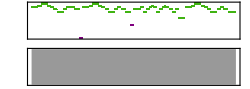

```mathematica
seq[{
3,3,4,5,
5,4,3,2,
1,1,2,3,
{Subscript[3, 3],Subscript[2, 1],2},2,"Snare",

3,3,4,5,
5,4,3,2,
1,1,2,3,
{Subscript[2, 3],Subscript[1, 1],2},1,"CrashCymbal",

2,2,3,1,
2,{Subscript[3, 1],Subscript[4, 1],1},3,1,
2,{Subscript[3, 1],Subscript[4, 1],1},3,2,
1,2,Subscript[(-2), 2],

3,3,4,5,
5,4,3,2,
1,1,2,3,
{Subscript[2, 3],Subscript[1, 1],2},Subscript[1, 2]

},18]//playSong
```

#### Hot Cross Buns

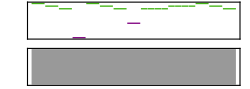

```mathematica
playSong[seq[{
3,2,1,"Snare",
3,2,1,"CrashCymbal",
f[{1,1,1,1},2],
f[{2,2,2,2},2],
3,2,1,r
},8]]
```

#### Itsy Bitsy Spider

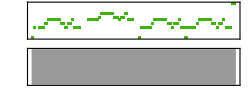

```mathematica
seq[{-2,
1,r,1,Subscript[1, 2],2,
Subscript[3, 3],Subscript[3, 2],3,
Subscript[2, 2],1,Subscript[2, 2],3,
Subscript[1, 3],Subscript[r, 3],

Subscript[3, 3],Subscript[3, 2],4,
Subscript[5, 3],Subscript[5, 3],
Subscript[4, 2],3,Subscript[4, 2],5,
Subscript[3, 3],Subscript[r, 2],

-2,
Subscript[1, 3],Subscript[1, 2],2,
Subscript[3, 3],Subscript[3, 3],
Subscript[2, 2],1,Subscript[2, 2],3,
Subscript[1, 3],

-Subscript[2, 2],-2,
Subscript[1, 2],1,Subscript[1, 2],2,
Subscript[3, 3],Subscript[3, 2],3,
Subscript[2, 2],1,Subscript[2, 2],3,
Subscript[1, 3],Subscript[8, 2],r
},12]//playSong
```